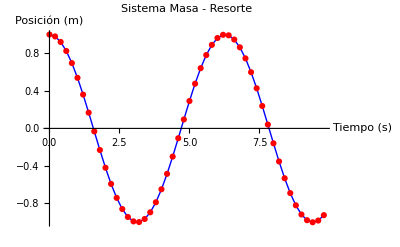

```mathematica
Verlet[a_,x0_,v0_,dt_,Ns_]:=Module[{xout,xnext,xcur,xprev,t,index},xout=Table[0.0,{j,1,Ns}];
xcur=x0;
xprev=x0-dt v0+(1/2) a[x0,0.0] dt^2;
t=0.0;
xout[[1]]={t,x0};
For[index=2,index≤Ns,index=index+1,xnext=2.0 xcur-xprev+dt^2 a[xcur,t];
t=t+dt;
xout[[index]]={t,xnext};
xprev=xcur;
xcur=xnext;];
Return[xout];]

(*Ley de Hooke:F=-k*x,por tanto a=F/m=-(k/m)*x*)
(*Suponiendo k/m=1 por comodidad*)
a[x_,t_]:=-x

(*Parámetros del sistema masa-resorte:*)

x0=1.0;(*posición inicial=1*)v0=0.0;(*velocidad inicial:reposo*)dt=0.2;(*cambio respecto al tiempo*)Ns=50;(*Número de iteraciones*)(*Ejecutamos*)resultados=Verlet[a,x0,v0,dt,Ns];

(*Gŕafica del Sistema Masa-Resorte*)
ListPlot[resultados,(*Realiza la gráfica en base a los resultados*)Joined->True,(*Conecta todos los puntos de tal forma sea continuo*)Mesh->All,(*Muestra todos los puntos*)AxesLabel->{"Tiempo (s)","Posición (m)"},(*Etiquetas para {x,t}*)PlotLabel->"Sistema Masa - Resorte",(*Título*)PlotStyle->{Blue,Thick},MeshStyle->Red]  (*Color y estilo de los puntos*)

(*TABLA:Resultados*)

Print["Tabla de resultados (primeros 5 valores):"];(*Título*)TableForm[Take[resultados,5],TableHeadings->{None,{"Tiempo (s)","Posición (m)"}} (*Crea la tabla con nombre para {x,t}*)
```